```mathematica
Clear["`*"];
```

```mathematica
realItpr=Interpreter["Real"];
```

```mathematica
jsonl=Import["~/okx.jsonl","String"];
lines=StringSplit[jsonl,"\n"];
```

```mathematica
parseLine[line_]:=Module[{json,time,response,btcNetwork,gasFee,usdGasFee},
json=Developer`ReadRawJSONString[line];
time=json["now"];
response=json["response"];
btcNetwork=Select[response["data","networks"],#["name"]=="BTC-Bitcoin"&][[1]];
gasFee=realItpr[btcNetwork["gasFee"]];
usdGasFee=realItpr[btcNetwork["usdGasFee"]];
{FromUnixTime[time],gasFee,usdGasFee}
];
```

```mathematica
parsed=parseLine/@lines;
```

```mathematica
parsedDedupe=Module[{p},
p[a_,b_]:={a[[2]],a[[3]]}=={b[[2]],b[[3]]};
DeleteAdjacentDuplicates[parsed,p]
];
```

```mathematica
data1=parsedDedupe//{#[[1]],#[[2]]}&/@#&;
data2=parsedDedupe//{#[[1]],#[[3]]}&/@#&;
```

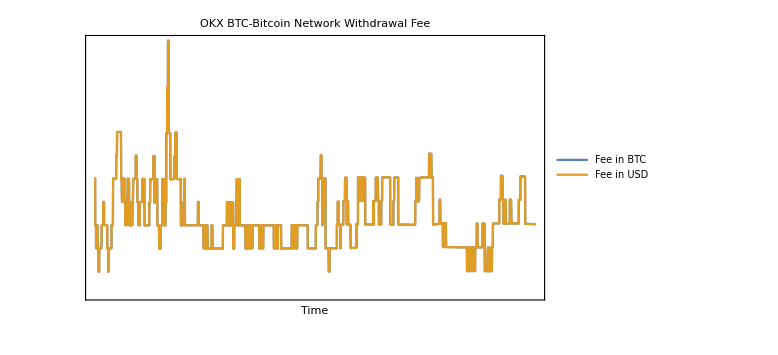
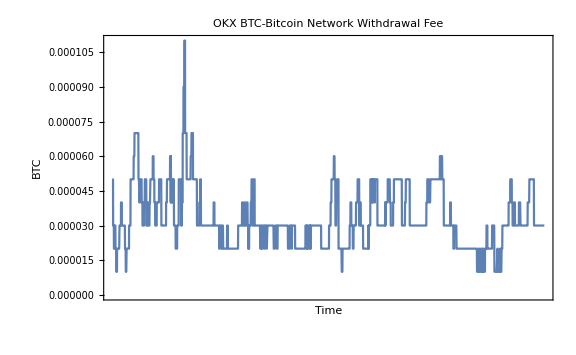

```mathematica
imagePadding={{70,70},{40,20}};
plotLabel="OKX BTC-Bitcoin Network Withdrawal Fee";
(*xTicks=Module[{start,end,range,fragments=7,increment},
start=parsedDedupe[[1,1]];
end=parsedDedupe[[-1,1]];
range=end-start;
increment=range/fragments;
start + increment (# - 1)& /@ Table[n, {n, fragments+1}]
];*)
tickFormat[date_]:=DateString[date,{"MonthNameShort"," ","Day","\n","Hour24",":","Minute"}]//StringReplace[#,"\\n"->"\n"]&;
xTicks=Module[{start,end,oneHourTicks},
end=parsedDedupe[[-1,1]];
start=DateObject[DateValue[parsedDedupe[[1,1]],{"Year","Month","Day","Hour24"}]]+Quantity[1, "Hours"];
oneHourTicks=Table[{n,Placeholder},{n,start,end,Quantity[1,"Hours"]}];
MapIndexed[(
{#1[[1]],If[Mod[#2[[1]]-1,4]==0,tickFormat@#1[[1]],""],If[Mod[#2[[1]]-1,4]==0,8,3]}
)&,oneHourTicks]
];
Overlay[{
DateListPlot[{data2,data2},
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
Axes->False,
ImagePadding->imagePadding,
ImageSize->Large,
FrameLabel->{{None,"USD"},{"Time",None}},
PlotLabel->plotLabel,
PlotLegends->{"Fee in BTC","Fee in USD"},
PlotRange->All,
DateTicksFormat -> {"MonthNameShort", " ", "Day", "\n", "Hour24",":", "Minute"}
],
DateListPlot[data1,
Frame->{{True,False},{True,True}},
ImagePadding->imagePadding,
ImageSize->Large,
FrameLabel->{{"BTC",None},{"Time",None}},
PlotLabel->plotLabel,
PlotRange->All,
DateTicksFormat -> {"MonthNameShort", " ", "Day", "\n", "Hour24",":", "Minute"},
FrameTicks->{{Automatic,None},{xTicks,Automatic}}
]
}]
```

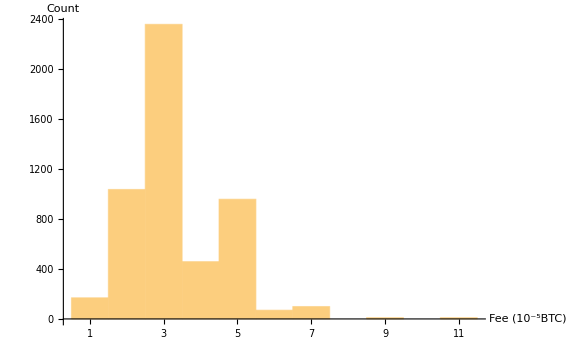

```mathematica
Module[{data,xTicks},
data=parsed//#[[2]]*10^5&/@#&;
xTicks=Table[x,{x,1,Max@data}];
Histogram[data,Automatic,"Count",
Ticks->{xTicks,All},
AxesLabel->{"Fee (10^-5BTC)",Count},
ImageSize->Large
]
]
```